```mathematica
dir=NotebookDirectory[]
SetDirectory[dir];
```

/Users/stefanhallermann/Desktop/github/sequential/out/

## traces

File number: 1

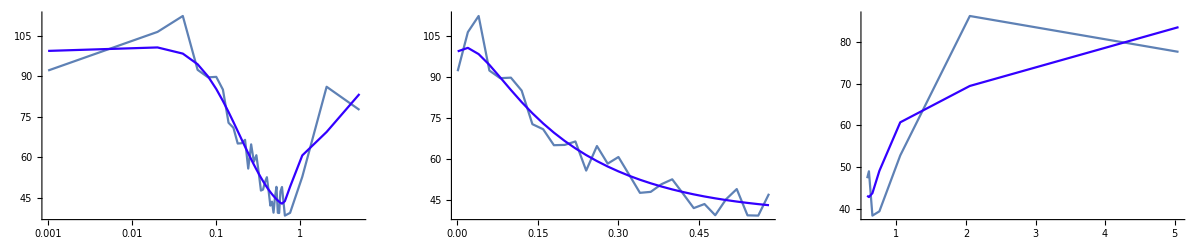

File number: 2

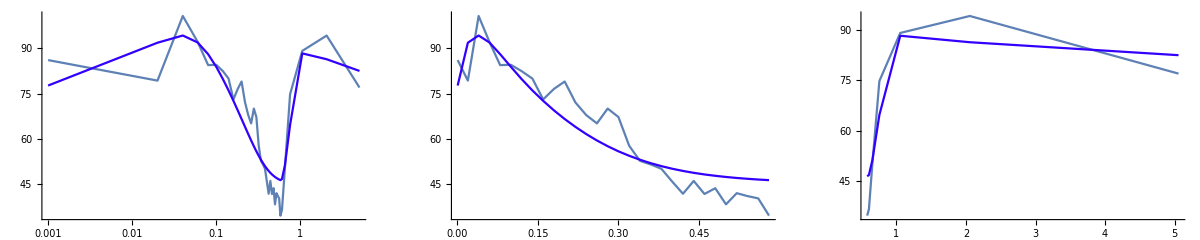

File number: 3

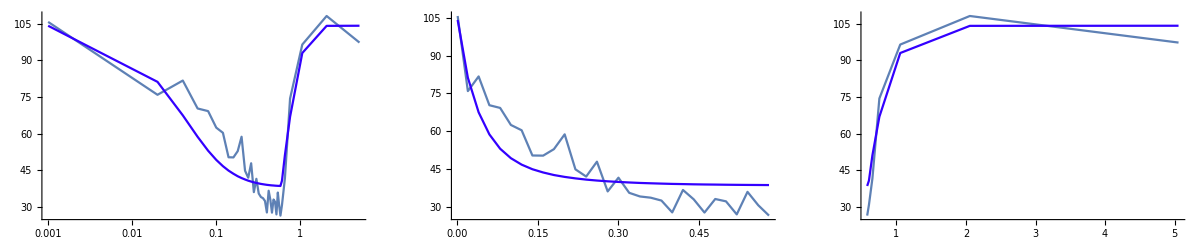

File number: 4

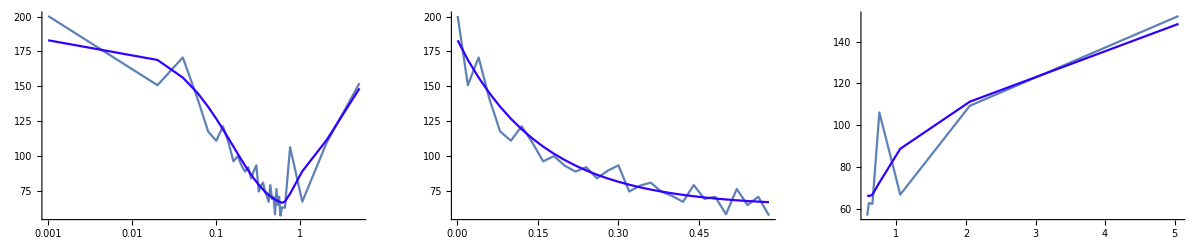

File number: 5

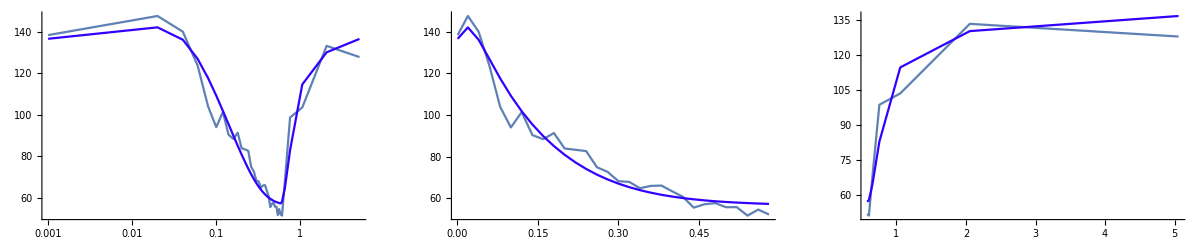

File number: 6

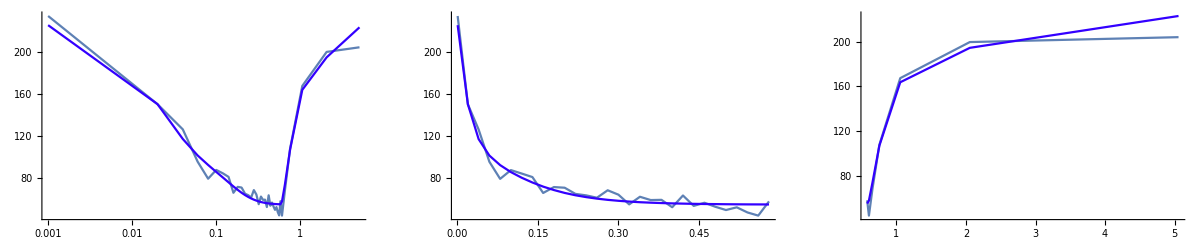

```mathematica
time300=Flatten[Import["time300.txt","Table"]];
time300[[1]]+=0.001;
tmp300=Import["apAmp300.txt","Table"];
tmpSim300=Import["apAmp300Sim.txt","Table"];
numFiles=Length[tmp300[[1,All]]];

t300t1=25;
t300t2=34;
train=30;
plR={All,All};

For[i=1,i≤numFiles,i+=1,
amp300=tmp300[[All,i]];
ampSim300=tmpSim300[[All,i]];
Print["File number: ",i];
(*log*)
tmp1=ListLogLinearPlot[Transpose[{time300,amp300}],PlotRange->All,Joined->True,DisplayFunction -> Identity];
tmp2=ListLogLinearPlot[Transpose[{time300,ampSim300}],PlotRange->All,Joined->True,PlotStyle->Hue[0.7],DisplayFunction -> Identity];
gr300=Show[{tmp1,tmp2},PlotRange->plR,DisplayFunction -> Identity];
(*train*)
tmp1=ListPlot[Take[Transpose[{time300,amp300}],train],PlotRange->All,Joined->True,DisplayFunction -> Identity];
tmp2=ListPlot[Take[Transpose[{time300,ampSim300}],train],PlotRange->All,Joined->True,PlotStyle->Hue[0.7],DisplayFunction -> Identity];
gr300tr=Show[{tmp1,tmp2},PlotRange->plR,DisplayFunction -> Identity];
(*recovery after train*)
tmp1=ListPlot[Take[Transpose[{time300,amp300}],{train,Length[time300]}],PlotRange->All,Joined->True,DisplayFunction -> Identity];
tmp2=ListPlot[Take[Transpose[{time300,ampSim300}],{train,Length[time300]}],PlotRange->All,Joined->True,PlotStyle->Hue[0.7],DisplayFunction -> Identity];
gr300rec=Show[{tmp1,tmp2},PlotRange->plR,DisplayFunction -> Identity];
Print[GraphicsGrid[{{gr300,gr300tr,gr300rec}}]];
];
```

## rates and chi2

```mathematica
tmp=Import["rates.txt","Table"];
Flatten[{{{"k10","b1","k20","b2","p_rel","chi2_train"}},tmp},1]//MatrixForm
```

(k10 | b1 | k20 | b2 | p_rel | chi2_train
0.142178 | 0.138773 | 1.47235 | 1.52941 | 0.128606 | 11.341
0.456871 | 0.588042 | 0.022476 | 0.0786887 | 0.296175 | 13.8975
8.04973 | 45.8875 | 8.83813 | 15.0418 | 0.547375 | 15.105
13.255 | 5.51887 | 0.372036 | 4.77665×10^-6 | 0.0775152 | 41.8876
2.12338 | 1.61739 | 0.670784 | 1.79347 | 0.330493 | 10.8711
2.04407 | 3.10306 | 0.507379 | 1.22912 | 0.676784 | 13.3794)